```mathematica
n=10;
F0=Fibonacci[n];
F1=Fibonacci[n-1];
F2=Fibonacci[n-2];
```

```mathematica
m=Table[1,{i,F0},{j,F0}];
```

```mathematica
(* construct recursively the matrix *)
recur[{m1_,m2_,m3_,n2_}]:=Block[{m},
(* create the new m2 array *)
m=ConstantArray[0,{Fibonacci[n2+2],Fibonacci[n2+2]}];

(* fill the 4 molecular clusters *)
m[[1;;Fibonacci[n2],1;;Fibonacci[n2]]]=m2;
m[[1;;Fibonacci[n2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],1;;Fibonacci[n2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;

(* fill the atomic cluster *)
m[[Fibonacci[n2]+1;;Fibonacci[n2+1],Fibonacci[n2]+1;;Fibonacci[n2+1]]]=m3;

{m,m1,m2,n2+1}]
```

```mathematica
m10={{1,1,0,1,1},{1,1,0,1,1},{0,0,1,0,0},{1,1,0,1,1},{1,1,0,1,1}};
m20={{1,0,1},{0,1,0},{1,0,1}};
m30={{1,1},{1,1}};
n0=4;
```

```mathematica
{m1,m2,m3,n}=recur[{m10,m20,m30,n0}];
```

```mathematica
{m1,m2,m3,n}=recur[{m1,m2,m3,n}];
```

```mathematica
ClearAll[recur]
```

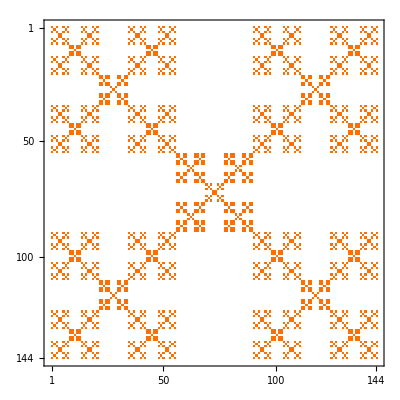

```mathematica
m2//MatrixPlot
```

```mathematica
Fibonacci[6]
```

8

```mathematica
recur[{m2,m3,n}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

{{1,0,1},{0,1,0},{1,0,1}}

{{{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1}},{{1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1},{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1}},8}

{{1,0,1},{0,1,0},{1,0,1}}

{{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},{{1,0,1},{0,1,0},{1,0,1}},0,0,0,0,0,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1}}